## Appendix E: Calculations for the Case of Deformation Without Displacement

## Preliminary Calculations: Determining the Variables

#### Define the deformation in terms of variables θ, ρ, p :

```mathematica
θ=-π/4;p=0.25;ρ=0.5;
```

#### Define z(x,y), zz(x,y):

```mathematica
z[x_,y_]:=x^2+y^2/ρ^2;
zz[x_,y_]:=x^2(Cos[θ]^2/p^2+(p^2 Sin[θ]^2)/ρ^2)+2x y Sin[θ]Cos[θ](1/p^2-p^2/ρ^2)+y^2(Sin[θ]^2/p^2+(p^2 Cos[θ]^2)/ρ^2);
Finit[x_,y_]:= 1/π*E^(-z[x,y]);
Ffinal[x_,y_]:= 1/π*E^(-zz[x,y]);
```

#### Normalization of wave packets W1 and W2

```mathematica
W1[x_,y_]=Finit[x,y]*(1/Integrate[Finit[x,y],{x,-∞,∞},{y,-∞,∞}]);
W2[x_,y_]=Ffinal[x,y]*(1/Integrate[Ffinal[x,y],{x,-∞,∞},{y,-∞,∞}]);
```

#### *Check for normalization

```mathematica
If[(Integrate[W1[x,y],{x,-∞,∞},{y,-∞,∞}]==1) && (Integrate[W2[x,y],{x,-∞,∞},{y,-∞,∞}]==1),Print[Style["Both wavefunctions are normalized.",15,Red]],Print[Style["Error: check normalization",18,Red]]]
```

Both wavefunctions are normalized.

#### Plot the distribution before and after deformation

```mathematica
GraphicsRow[{Plot3D[W1[x,y],{x,-4,4},{y,-4,4},PlotRange->All],Plot3D[W2[x,y],{x,-4,4},{y,-4,4},PlotRange->All]}]
```

-Graphics-

#### Define aa, bb and cc from the expression of zz(x,y):

```mathematica
aa=(Cos[θ]^2/p^2+(p^2 Sin[θ]^2)/ρ^2);
bb=2*Sin[θ]Cos[θ](1/p^2-p^2/ρ^2);
cc=(Sin[θ]^2/p^2+(p^2 Cos[θ]^2)/ρ^2);
```

#### Calculating values for slopes m1 & m2:

```mathematica
dir1=(-bb+√(bb^2-4*(aa-1)*(cc-1/ρ^2)))/(2*(cc-1/ρ^2));
dir2=(-bb-√(bb^2-4*(aa-1)*(cc-1/ρ^2)))/(2*(cc-1/ρ^2));
```

#### Calculating values for slopes ma & mb:

```mathematica
result1=(-1+dir1*dir2+√((1+dir1^2)*(1+dir2^2)))/(dir1+dir2);
result2=(-1+dir1*dir2-√((1+dir1^2)*(1+dir2^2)))/(dir1+dir2);
```

#### Determining the positivity of all four slopes

```mathematica
(*decide the values for ma & mb*)If[result1>0,{ma=result1,mb=result2},{ma=result2,mb=result1}];
```

```mathematica
(*decide the values for m1 & m2*)
If[mb<dir2<ma,{m1=dir1,m2=dir2},{m1=dir2,m2=dir1}];
```

#### Plotting the slopes (m1, m2, ma, mb)

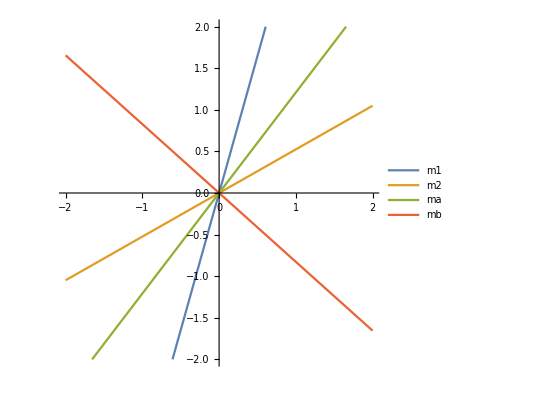

```mathematica
Plot[{m1*x,m2*x,ma*x,mb*x},{x,-2,2},
PlotLegends->{"m1","m2","ma","mb"}, PlotRange->{-2,2},
AspectRatio->1]
```

## Finding the Transport and Price Functions

#### Region 1:

```mathematica
(*transportation function f(i,j,k,l)*)
c11=(m1+m2)/(m1-m2);
c12=-2/(m1-m2);
c13=(2*m1*m2)/(m1-m2);
c14=(-(m1+m2))/(m1-m2);
f1[i_,j_,k_,l_]:=(W1[i,j]-W2[i,j])*DiracDelta[k-(c11*i+c12*j)]*DiracDelta[l-(c13*i+c14*j)];
(*cost function u(x,y)*) u1[x_,y_]:=(1/(√(1+m1^2)))*(x+m1*y);
```

#### Region 2:

```mathematica
(*transportation function f(i,j,k,l)*)
c21=(m2+m1)/(m2-m1);
c22=-2/(m2-m1);
c23=(2*m2*m1)/(m2-m1);
c24=(-(m2+m1))/(m2-m1);
f2[i_,j_,k_,l_]:=(W1[i,j]-W2[i,j])*DiracDelta[k-(c21*i+c22*j)]*DiracDelta[l-(c23*i+c24*j)];
(*Finding the cost function u(x,y)*) u2[x_,y_]:=(1/(√(1+m2^2)))*(x+m2*y);
```

## Calculating the solution

```mathematica
(*decide the positivity for [W1(i,j) - W2(i,j)] for transportation cost calculation*)
diff=NIntegrate[W1[i,j]-W2[i,j],{i,0,∞},{j,mb*i,m2*i}];
If[diff>0,{WDiff[i,j]=W1[i,j]-W2[i,j]},{WDiff[i,j]=W2[i,j]-W1[i,j]}];
```

#### The transportation cost for region 1:

```mathematica
TransCost1=NIntegrate[WDiff[i,j]*√((c11*i+c12*j-i)^2+(c13*i+c14*j-j)^2),{i,0,∞},{j,mb*i,m2*i}]
```

0.303643

#### The transportation cost for region 2:

```mathematica
TransCost2=NIntegrate[WDiff[i,j]*√((c21*i+c22*j-i)^2+(c23*i+c24*j-j)^2),{j,0,∞},{i,j/mb,j/m1}]
```

0.077542

```mathematica
(*decide the positivity for [W1(i,j) - W2(i,j)] for dual cost calculation*)
diff=NIntegrate[W1[i,j]-W2[i,j],{i,0,∞},{j,mb*i,ma*i}];
If[diff>0,{WDiff[i,j]=W1[i,j]-W2[i,j]},{WDiff[i,j]=W2[i,j]-W1[i,j]}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 7.17309×10^-17 and 1.26716×10^-13 for the integral and error estimates.

#### The dual cost for region 1:

```mathematica
DualCost1=Abs[NIntegrate[WDiff[i,j]*u1[i,j],{i,0,∞},{j,mb*i,ma*i}]]
```

0.303643

#### The dual cost for region 2:

```mathematica
DualCost2=Abs[NIntegrate[WDiff[i,j]*u2[i,j],{j,0,∞},{i,j/mb,j/ma}]]
```

0.077542

## Total Cost

#### Total transportation cost

The transportation cost for region 3 is identical to region 1, and region 4 is identical to region 2 due to symmetry.

```mathematica
TransCost=2*(TransCost1+TransCost2)
```

0.76237

```mathematica
NumberForm[TransCost,16]
```

0.7623699396015978

#### Total dual cost

The dual cost for region 3 is identical to region 1, and region 4 is identical to region 2 due to symmetry.

```mathematica
DualCost=2*(DualCost1+DualCost2)
```

0.76237

```mathematica
NumberForm[DualCost,16]
```

0.7623699588057274